```mathematica
Exit[]
```

```mathematica
M[F_]:=(R-r F)/d[F]
```

```mathematica
d[F_]:=d0
```

```mathematica
s=DSolve[{D[F[n],n]==(-M[F[n]])/n,F[n0]==F0},F[n],n]
```

{{F[n]→(n0^(-r/d0) (F0 n^(r/d0) r-n^(r/d0) R+n0^(r/d0) R))/r}}

```mathematica
(*Stock price:*)
Simplify[M[F[n]]/n/.s[[1,1]]]
```

(n^(-1+r/d0) n0^(-r/d0) (-F0 r+R))/d0

```mathematica
d[F_]:=-(1/(1-r F/R))^k+r
```

```mathematica
s=DSolve[{D[F[n],n]==(-M[F[n]])/n,F[n0]==F0},F[n],n]
```

{{F[n]→InverseFunction[Log[-R+r #1]+((-1)^k R^k (-R+r #1)^-k)/(k r)&][Log[n]-((F0 r-R)^-k (-(-1)^k R^k+k r (F0 r-R)^k Log[n0]-k r (F0 r-R)^k Log[F0 r-R]))/(k r)]}}

```mathematica
S=Simplify[M[F[n]]/n/.s[[1,1]]]
```

(-R+r InverseFunction[Log[-R+r #1]+((-1)^k R^k (-R+r #1)^-k)/(k r)&][((-1)^k (F0 r-R)^-k R^k)/(k r)+Log[n]-Log[n0]+Log[F0 r-R]])/(n (-r+(R/(R-r InverseFunction[Log[-R+r #1]+((-1)^k R^k (-R+r #1)^-k)/(k r)&][((-1)^k (F0 r-R)^-k R^k)/(k r)+Log[n]-Log[n0]+Log[F0 r-R]]))^k))

```mathematica
S2=Simplify[S/.R->1/.k->-10/.r->0.03/.n->x n0/.n0->100/.F0->0]
```

(-1.+0.03 InverseFunction[Log[-1+0.03 #1]+(-1+0.03 #1)^(-(-10))/((-1)^10 (-10) 0.03 1^10)&][(-3.33333+3.14159 ⅈ)+Log[x]])/(100 x (-0.03+(1-0.03 InverseFunction[Log[-1+0.03 #1]+(-1+0.03 #1)^(-(-10))/((-1)^10 (-10) 0.03 1^10)&][(-3.33333+3.14159 ⅈ)+Log[x]])^10))

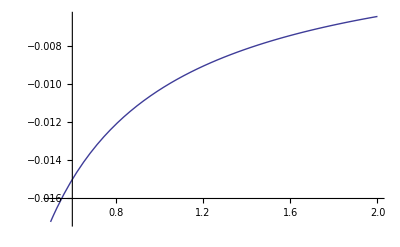

```mathematica
Plot[S2,{x,0.5,2}]
```